1. Задаем начальные данные :

```mathematica
X1={1/10, 3/10, 7/10, 14/10}; F={1, -7, 15, 25};
```

```mathematica
n=Length[X1]-1;
```

```mathematica
Do[{Subscript[x, i]=X1[[i+1]],Subscript[f, i]=F[[i+1]]},{i,0,n}]
```

2. Строим интерполяционный  сплайн:

```mathematica
Subscript[Pa, k_][X_]=Subscript[f, k]+(X-Subscript[x, k])*Subscript[A, k];
eqv1a=Table[Subscript[Pa, k][Subscript[x, k+1]]==Subscript[Pa, k+1][Subscript[x, k+1]],{k,0,n-2}];
eqv2a={Subscript[Pa, n-1][Subscript[x, n]]==Subscript[f, n]};
eqva= Join[eqv1a, eqv2a];
koefa=Solve[eqva,{}]//Flatten
Spla[x_]=Table[Subscript[Pa, k][x]/.koefa,{k,0,n-1}]//Expand;
```

{A_0→-40,A_1→55,A_2→100/7}

```mathematica
Subscript[Pb, k_][X_]=Subscript[f, k]+(X-Subscript[x, k])*(Subscript[A, k]*X+Subscript[B, k]);
eqv1b=Table[Subscript[Pb, k][Subscript[x, k+1]]==Subscript[Pb, k+1][Subscript[x, k+1]],{k,0,n-2}];
eqv2b={Subscript[Pb, n-1][Subscript[x, n]]==Subscript[f, n]};
Subscript[PPb, k_][X_]=D[Subscript[Pb, k][X], X];
eqv3b=Table[Subscript[PPb, k][Subscript[x, k+1]]==Subscript[PPb, k+1][Subscript[x, k+1]],{k,0,n-2}];
eqv4b={Subscript[Pb, 0]'[Subscript[x, 0]]==0};
eqvb= Join[eqv1b, eqv2b, eqv3b,eqv4b];
koefb=Solve[eqvb,{}]//Flatten;
Splb[x_]=Table[Subscript[Pb, k][x]/.koefb,{k,0,n-1}]//Expand
```

{-1+40 x-200 x^2,379/8-(565 x)/2+(675 x^2)/2,-241+(3790 x)/7-(12300 x^2)/49}

```mathematica
Subscript[Pc, k_][X_]=Subscript[f, k]+(X-Subscript[x, k])*(Subscript[A, k]*X^2+Subscript[B, k]*X+Subscript[C1, k]);
eqv1c=Table[Subscript[Pc, k][Subscript[x, k+1]]==Subscript[Pc, k+1][Subscript[x, k+1]],{k,0,n-2}];
eqv2c={Subscript[Pc, n-1][Subscript[x, n]]==Subscript[f, n]};
Subscript[PPc, k_][X_]=D[Subscript[Pc, k][X], X];
eqv3c=Table[Subscript[PPc, k][Subscript[x, k+1]]==Subscript[PPc, k+1][Subscript[x, k+1]],{k,0,n-2}];
eqv4c={Subscript[Pc, 0]''[Subscript[x, 0]]==0};
Subscript[PPPc, k_][X_]=D[Subscript[Pc, k][X], X,X];
eqv5c=Table[Subscript[PPPc, k][Subscript[x, k+1]]==Subscript[PPPc, k+1][Subscript[x, k+1]],{k,0,n-2}];
eqv6c={Subscript[Pc, n-1]''[Subscript[x, n]]==0};
eqvc= Join[eqv1c, eqv2c, eqv3c,eqv4c,eqv5c,eqv6c];
koefc=Solve[eqvc,{}]//Flatten;
Splc[x_]=Table[Subscript[Pc, k][x]/.koefc,{k,0,n-1}]//Expand
```

{22091/3472-(77325 x)/1736-(118275 x^2)/868+(197125 x^3)/434,26905/992-(875415 x)/3472+(964725 x^2)/1736-(273125 x^3)/868,-3037/31+(61620 x)/217-(45600 x^2)/217+(76000 x^3)/1519}

3. Проверяем выполнение интерполяционных условий:

```mathematica
Join[Table[Spla[Subscript[x, i]][[i+1]]==Subscript[f, i],{i,0,n-1}], {Spla[Subscript[x, n]][[n]]==Subscript[f, n]}]
Join[Table[Splb[Subscript[x, i]][[i+1]]==Subscript[f, i],{i,0,n-1}], {Splb[Subscript[x, n]][[n]]==Subscript[f, n]}]
Splb'[Subscript[x, 0]][[1]]==0
Join[Table[Splc[Subscript[x, i]][[i+1]]==Subscript[f, i],{i,0,n-1}], {Splc[Subscript[x, n]][[n]]==Subscript[f, n]}]
{Splc'[Subscript[x, 0]][[1]]==0,Splc''[Subscript[x, n]][[n]]==0}
```

{True,True,True,True}

{True,True,True,True}

True

{True,True,True,True}

{False,True}

4. Изображаем исходную систему точек и полученный интерполяционный многочлен в одной системе координат:

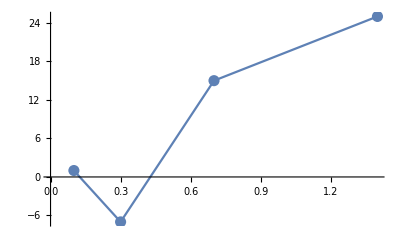

```mathematica
Tb1=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}];
Gr1=ListPlot[Tb1,PlotStyle->{PointSize[0.02]}];
Gr2a=Table[Plot[Spla[x][[k]],{x,Subscript[x, k-1],Subscript[x, k]}],{k,1,n}];
Show[Gr1,Gr2a]
```

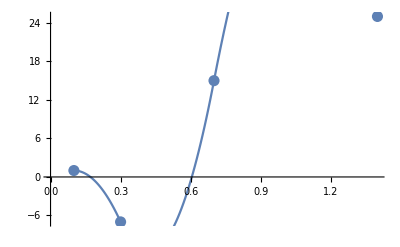

```mathematica
Gr2b=Table[Plot[Splb[x][[k]],{x,Subscript[x, k-1],Subscript[x, k]}],{k,1,n}];
Show[Gr1,Gr2b]
```

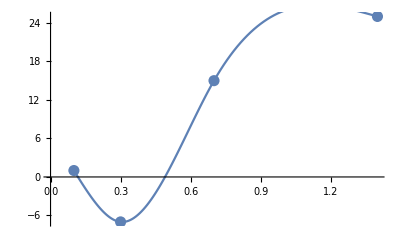

```mathematica
Gr2c=Table[Plot[Splc[x][[k]],{x,Subscript[x, k-1],Subscript[x, k]}],{k,1,n}];
Show[Gr1,Gr2c]
```

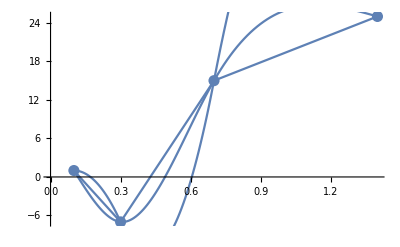

```mathematica
Show[Gr1,Gr2a, Gr2b,Gr2c]
```